# Hydrogen molecule: plotting.

## Fitting Morse potential function

```mathematica
Clear[min]
```

{0.8505,-3.13498}

1.34281

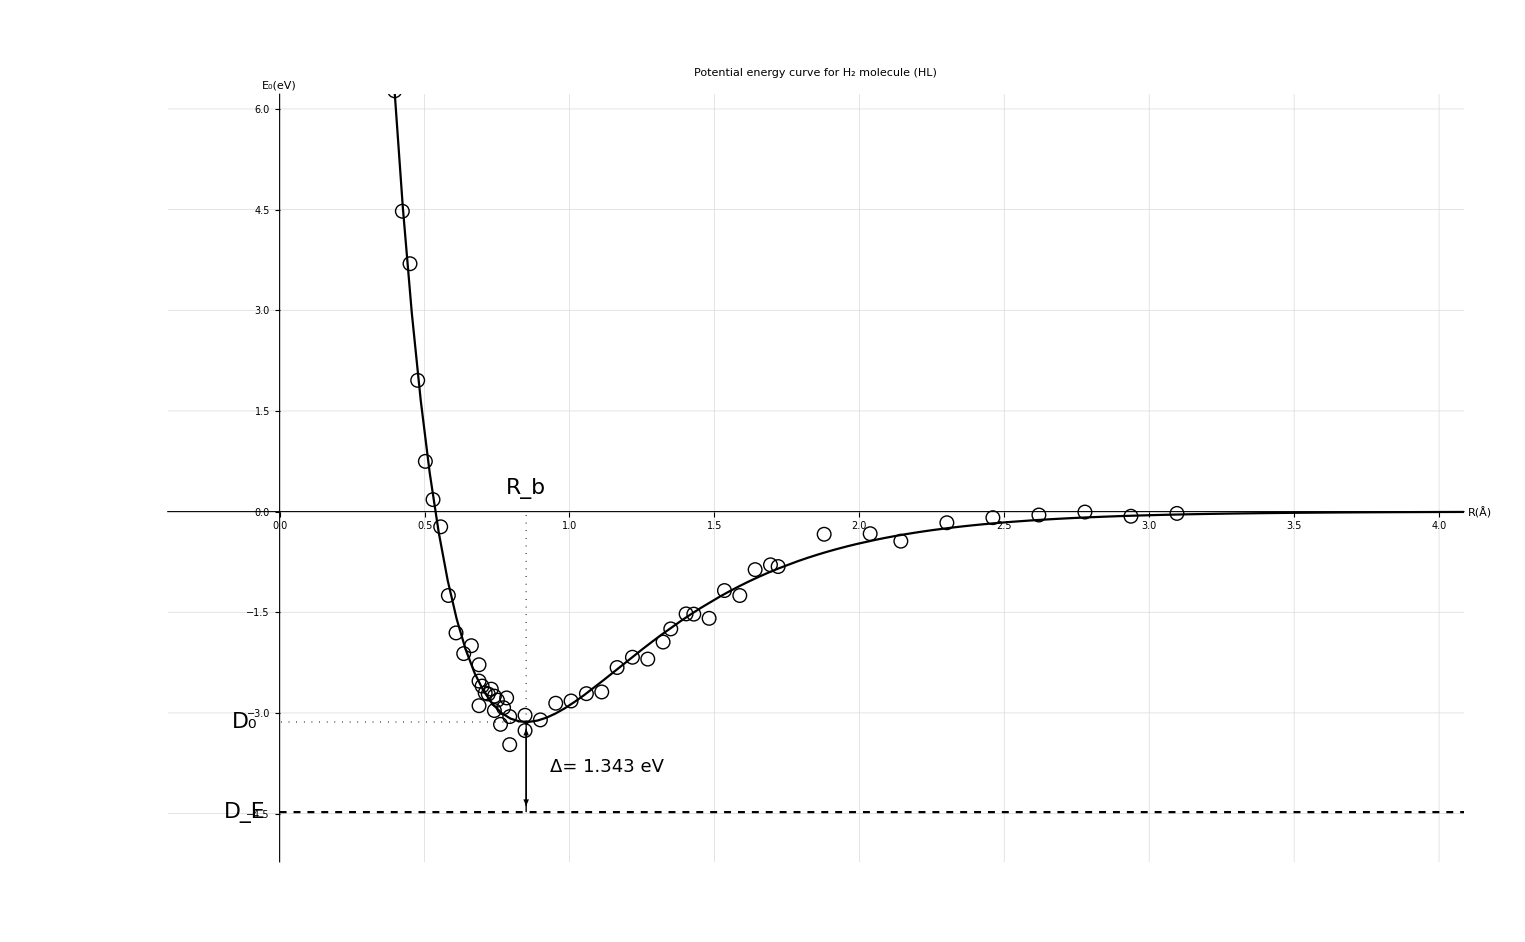

```mathematica
ClearAll["Global`*"];
data = Rest[Import[SystemDialogInput["FileOpen"]]];
D0exp = 4.4777954313;
H2unb=-27.211396132;
last=Last[data];
γb2A=0.52917725;
For[i=1,i<=Length[data],i++,
data[[i,1]]*=γb2A;
]
morse=a+b(Exp[-2*(x-c)/d]-2*Exp[-(x-c)/d]);
fit=FindFit[data,morse, {a, b, c, d}, x];
last = morse/.fit /.x-> 100;
For[i=1,i<=Length[data],i++,
data[[i,2]]-=last;
]
fit=FindFit[data,morse, {a, b, c, d}, x];
min1=FindMinimum[morse/.fit, x];
minX=min1[[2,1,2]];
minY=min1[[1]];
min1={minX,minY}
minPlot=Plot[minY, {x, 0, minX}, PlotStyle->{Dashed, Red}];
m=min1[[1]];
morsePlot=Plot[morse/. fit, {x, -1, 100}, PlotStyle->Black,PlotRange->{{-1, 50},{-5,10}}, PlotStyle->Thick, PlotLabel->Style["Potential energy curve for H_2 molecule", 18],LabelStyle->{FontFamily->"Saab",18,GrayLevel[0]}];
pointPlot=ListPlot[data,PlotStyle->Black, PlotRange->{{0,7}, Automatic}, PlotMarkers->{"○",14}];
experiment=Plot[-D0exp, {x,0, 7}, PlotStyle->{Dashed, Black}];
diff=D0exp+minY
Show[morsePlot,experiment,pointPlot, Graphics[{Arrowheads[{{1,1,Graphics@Style[Text["►",{0,0},{0,0}],FontSize->12]}}],Arrow[{min1,{min1[[1]],-D0exp+0.09}}]}], Graphics[{Arrowheads[{{1,1,Graphics@Style[Text["►",{0,0},{0,0}],FontSize->12]}}],Arrow[{{min1[[1]],-D0exp}, {min1[[1]],min1[[2]]-0.1}}]}],FrameLabel->{{Style["\!\(\*SubscriptBox[\(E\), \(0\)]\) [eV]"]},{Style["R [Å]"]}}, PlotRange->{{-0.3, 4},{-5,6}}, AxesLabel->{Style[HoldForm[R[Å]],22],Style[HoldForm[Subscript[Ε, 0][eV]],22]},FrameLabel->{{None,None},{None,None}},PlotLabel->Style[HoldForm[Potential energy curve for Subscript[H, 2] molecule" " [HL]],32],LabelStyle->{FontFamily->"URW Gothic L",GrayLevel[0]},AxesStyle->Thick,PlotRange->{{-0.3, 4},{-5,6}},ImagePadding->70,TicksStyle-> 20, GridLines->Automatic,Epilog->{PointSize[Large],Point[min1],Dotted,Line[{min1,{min1[[1]],0}}],Line[{min1,{0,min1[[2]]}}],Text[Style["R_b",22],{min1[[1]], 0.35}],Text[Style["D_0",22] ,{-.12, min1[[2]]}],Text[Style["Δ= 1.343 eV",18]  ,{min1[[1]]+0.28,(min1[[2]] -D0exp)/2}],Text[Style["D_E",22],{-0.12, -D0exp}]}]
```

```mathematica
{0.8505001372688124,-3.1349826586145904}
```

1.34281

```mathematica
Epilog->{PointSize[Large],Point[min],Dotted,Line[{min,{min[[1]],0}}],Line[{min,{0,min[[2]]}}],Text[Style["R_b",14],{min[[1]], 0.35}],Text[Style["D_0",14] ,{-.12, min[[2]]}],Text[Style["Δ= 1.343 eV",14]  ,{min[[1]]+0.23,(min[[2]] -D0exp)/2}],Text[Style["D_E",14],{-0.12, -D0exp}]}
```

## Hartree-Fock treatment

{0.687934,-4.02345}

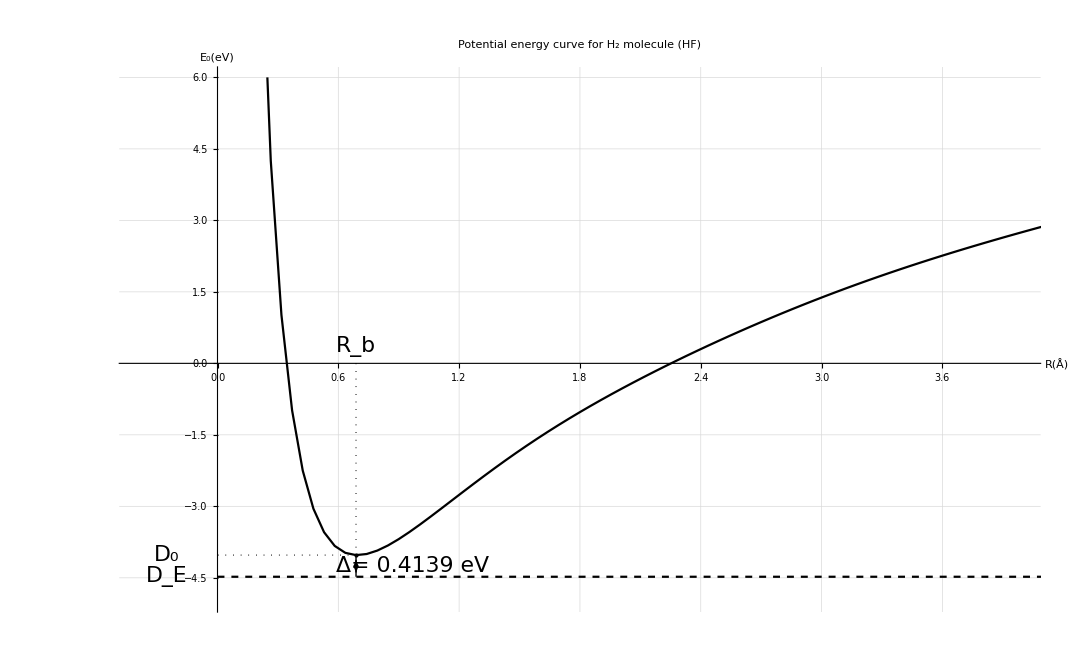

```mathematica
twohen=27.2116;
conv=4.477954313/31.9570;
conv2=4.477954313/1.174475712;
conv3=13.6058;
bohrtoA=0.52918;
D0exp=4.4777954313;
data=Import["/home/patlip/Dokumenty/H2/code/HF/Hartree-Fock/h2.out","Table"];
dataLength=Length[data];
R=Range[dataLength-1];
Eelec=Range[dataLength-1];
Enuc=Range[dataLength-1];
Etot=Range[dataLength-1];
Ebind=Range[dataLength-1];
For[i=1,i<dataLength,i++,R[[i]]=data[[i,1]];
Eelec[[i]]=data[[i,2]];
Enuc[[i]]=data[[i,3]];
Etot[[i]]=data[[i,4]];
Ebind[[i]]=data[[i,5]];]
npoints=(Floor[.1*dataLength]);
line=Transpose[{R,Etot-Last[Etot]}][[-npoints;;]];
fit=Fit[line,{1,x},x];
(*Show[ListPlot[line,PlotStyle->Red],Plot[fit,{x,line[[1,1]],line[[npoints-1,1]]}]]*)
For[i=1,i<dataLength,i++,R[[i]]=bohrtoA*data[[i,1]];
Eelec[[i]]=data[[i,2]];
Enuc[[i]]=data[[i,3]];
Etot[[i]]=conv3*((data[[i,4]])+1)-2;
Ebind[[i]]=data[[i,5]];]
min2={R[[Position[Etot,Min[Etot]][[1,1]]]],Min[Etot]}
p1=ListLinePlot[R];
p2=ListLinePlot[Transpose[{R,Eelec}]];
p3=ListLinePlot[Transpose[{R,Enuc}]];
p4=ListLinePlot[Transpose[{R,Etot}]];
p5=ListLinePlot[Transpose[{R,Ebind}]];
energyPlot=ListLinePlot[Transpose[{R,Etot}],PlotStyle->Black,PlotRange->{{-0.4,30},{-5,6}},PlotStyle->Thick,LabelStyle->{FontFamily->"Saab",20,GrayLevel[0]}];
Show[energyPlot,experiment, Graphics[{Arrowheads[{{1,1,Graphics@Style[Text["►",{0,0},{0,0}],FontSize->12]}}],Arrow[{min2,{min2[[1]],-D0exp+0.09}}]}], Graphics[{Arrowheads[{{1,1,Graphics@Style[Text["►",{0,0},{0,0}],FontSize->12]}}],Arrow[{{min2[[1]],-D0exp}, {min2[[1]],min2[[2]]-0.1}}]}],FrameLabel->{{Style["\!\(\*SubscriptBox[\(E\), \(0\)]\) [eV]"]},{Style["R [Å]"]}}, PlotRange->{{-0.4, 4},{-5,6}}, AxesLabel->{Style[HoldForm[R[Å]],22],Style[HoldForm[Subscript[Ε, 0][eV]],22]},FrameLabel->{{None,None},{None,None}},PlotLabel->Style[HoldForm[Potential energy curve for Subscript[H, 2] molecule " "[HF]],32],LabelStyle->{FontFamily->"URW Gothic L",GrayLevel[0]},AxesStyle->Thick,PlotRange->{{-0.3, 4},{-5,6}},ImagePadding->70,TicksStyle->22, GridLines->Automatic,Epilog->{PointSize[Large],Point[min2],Dotted,Line[{min2,{min2[[1]],0}}],Line[{min2,{0,min2[[2]]}}],Text[Style["R_b",22],{min2[[1]], 0.35}],Text[Style["D_0",22] ,{-.25, min2[[2]]}],Text[Style["Δ= 0.4139 eV",22]  ,{min2[[1]]+0.28,(min2[[2]] -D0exp)/2}],Text[Style["D_E",22],{-0.25, -D0exp}]}]
```

## Comparison (HL & HF)

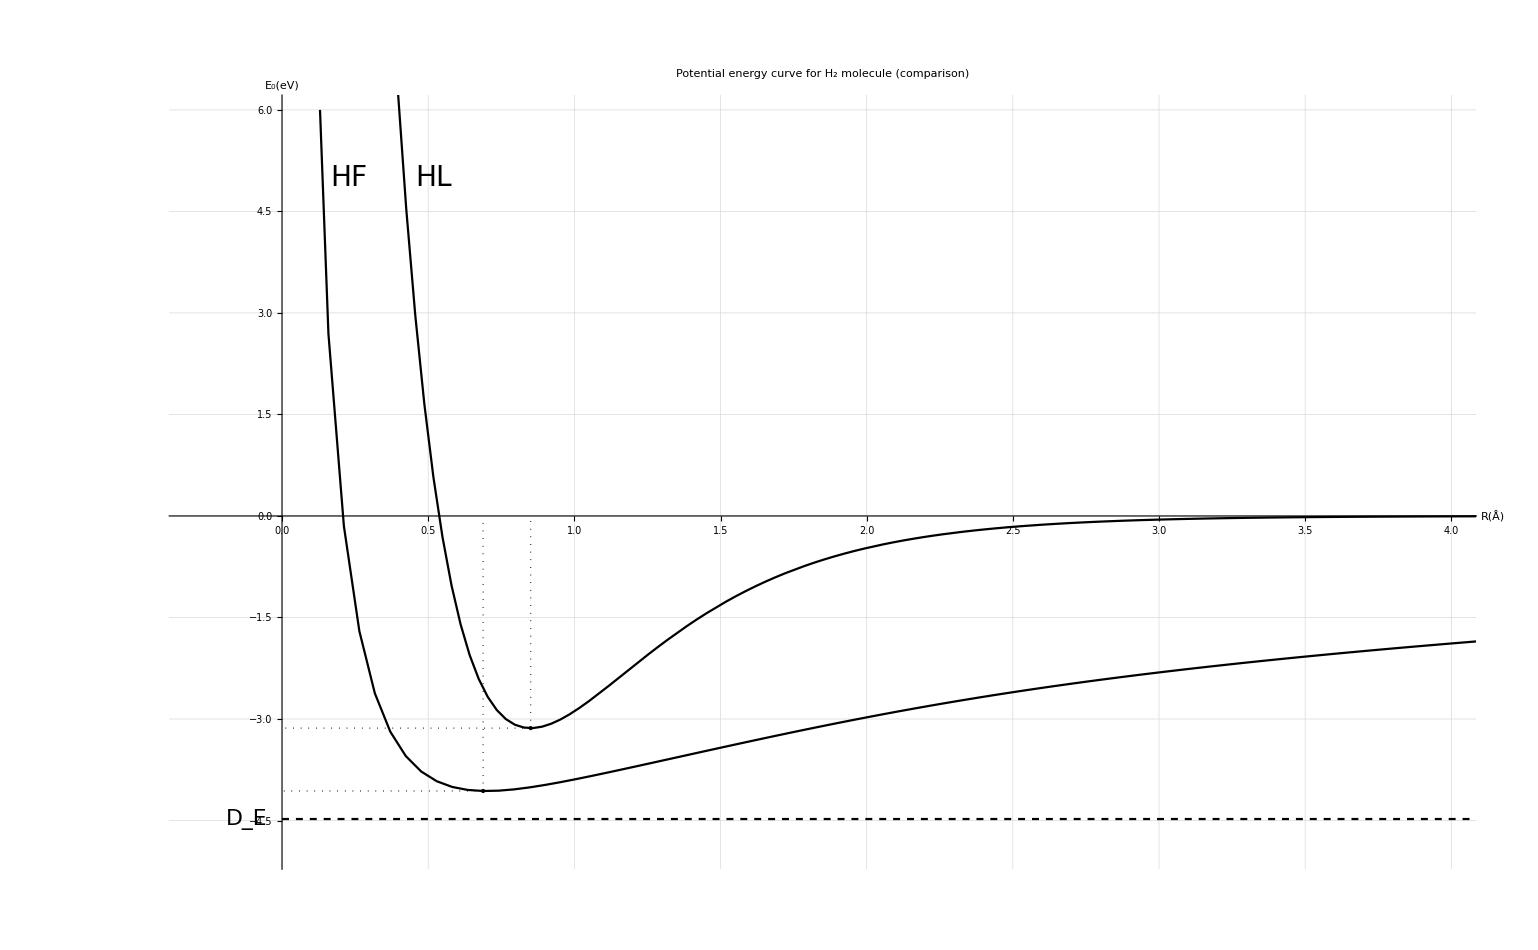

```mathematica
Show[energyPlot,morsePlot,experiment,AxesLabel->{Style[HoldForm[R[Å]],22],Style[HoldForm[Subscript[Ε, 0][eV]],22]},FrameLabel->{{None,None},{None,None}},PlotLabel->Style[HoldForm[Potential energy curve for Subscript[H, 2] molecule " "[comparison]],32],LabelStyle->{FontFamily->"URW Gothic L",GrayLevel[0]},AxesStyle->Thick,PlotRange->{{-0.3, 4},{-5,6}},PlotRange-> {{-.1, 50},Automatic}ImagePadding->70,TicksStyle->22, GridLines->Automatic,Epilog->{PointSize[Large],Point[min1],Dotted,Line[{min1,{min1[[1]],0}}],Line[{min1,{0,min1[[2]]}}],PointSize[Large],Point[min2],Dotted,Line[{min2,{min2[[1]],0}}],Line[{min2,{0,min2[[2]]}}],Text[Style["D_E",22],{-0.12, -D0exp}],Text[Style["HF",28],{0.23, 5}],Text[Style["HL",28],{0.52, 5}]}]
```

```mathematica
ShowLegend[Show[plot1,plot2],{{Graphics[{#1,Thick,Line[{{0,0},{1,0}}]}],#2}&@@@Transpose[{colors,legends}],LegendPosition->{-0.65,-0.5},LegendSpacing->0,LegendShadow->None,LegendSize->0.6}]
```